### The Double Power Series Method

The first part of the sheet calculates the double power series, and the associated matter perturbation
The double power series part can be easily adapted to deal with other similar (systems of) differential equations

INPUT the names of the functions in the (system of) differential equations (this is only for display purposes).

```mathematica
fncnames={ψ,Subscript[δ, r]};
```

INPUT the matrices for the differential equations (or scalars if only one differential equation - do not use 1x1 matrices).

```mathematica
a={{1,0},{-4,1}};
```

```mathematica
bm2={{0,0},{4/3,1/3}};
```

```mathematica
b0={{-16/(τ^2 (4+τ)^2),-8/(τ^2 (4+τ)^2)},{0,0}};
```

```mathematica
c={{(6 (2+τ))/(τ (4+τ)),0},{0,0}};
```

The next line isn’t necessary, but shows you the matrices you’ve input in a nice format.

```mathematica
displaymatrices[]
```

A=(1 | 0
-4 | 1), B_-2=(0 | 0
4/3 | 1/3), B_0=(-16/(τ^2 (τ+4)^2) | -8/(τ^2 (τ+4)^2)
0 | 0), C=((6 (τ+2))/(τ (τ+4)) | 0
0 | 0)

The next line gives you the eigenvalues of A^-1 B_-2.

```mathematica
inspecteigenvalues[]
```

{1/3,0}

The next line runs the Double Power Series method.  INPUT the eigenvalue you want it to use as the first argument of runDoublePowerSeries.  INPUT the maxmium value of s as the second argument.  The resulting functions displayed nicely and returned in “functions”.

```mathematica
functions=runDoublePowerSeries[1/3,3];
```

E(τ)=ⅇ^((ⅈ k τ)/(√3)+(4 ⅈ √3 (2+τ))/(k τ (4+τ))) (τ/(4+τ))^((ⅈ √3)/k)

ψ(τ)={(48 ⅈ √3 (2+τ))/(k^3 τ^3 (4+τ)^3)-24/(k^2 τ^2 (4+τ)^2)}*E(τ)

δ_r(τ)={1}*E(τ)

```mathematica
ψappr[τ_]:=Evaluate[functions[[1]]]
```

```mathematica
δrappr[τ_]:=Evaluate[functions[[2]]]
```

```mathematica
functions=runDoublePowerSeries[1/3,5];
```

E(τ)=ⅇ^((ⅈ k τ)/(√3)+(4 ⅈ √3 (2+τ))/(k τ (4+τ))-(288 (16+44 τ+11 τ^2))/(k^4 τ^4 (4+τ)^4)+(ⅈ √3 (-256-960 τ+624 τ^2+1144 τ^3+390 τ^4+39 τ^5))/(2 k^3 τ^3 (4+τ)^3)) (τ/(4+τ))^((ⅈ √3 (39+8 k^2))/(8 k^3))

ψ(τ)={-(5184 ⅈ √3 (2+τ))/(k^5 τ^4 (4+τ)^4)+864/(k^4 τ^3 (4+τ)^3)+(48 ⅈ √3 (2+τ))/(k^3 τ^3 (4+τ)^3)-24/(k^2 τ^2 (4+τ)^2)}*E(τ)

δ_r(τ)={1}*E(τ)

```mathematica
ψappr5[τ_]:=Evaluate[functions[[1]]]
```

```mathematica
δrappr5[τ_]:=Evaluate[functions[[2]]]
```

The next line calculates the matter perturbation.  INPUT the ψ and δ_r functions as the first two arguments.  INPUT the maxinum order n of k^-n which you want in the result.

```mathematica
δmappr[τ_]:=Evaluate[δmcalculate[ψappr5,δrappr5,δrappr,3]]
```

ⅇ^((ⅈ k τ)/(√3)+(4 ⅈ √3 (2+τ))/(k τ (4+τ))) (τ/(4+τ))^((ⅈ √3)/k) (-144/(k^2 τ^2 (4+τ)^2)+(720 ⅈ (2 √3+√3 τ))/(k^3 τ^3 (4+τ)^3))

```mathematica
δmappr[τ]
```

ⅇ^((ⅈ k τ)/(√3)+(4 ⅈ √3 (2+τ))/(k τ (4+τ))) (τ/(4+τ))^((ⅈ √3)/k) (-144/(k^2 τ^2 (4+τ)^2)+(720 ⅈ (2 √3+√3 τ))/(k^3 τ^3 (4+τ)^3))

The following graphs display the results

For the function in the next line INPUT the ψ and δ_r functions, followed by the value of k, the minimum and the maximum values of τ, and PlotRanges for the ψ and δ_r graphs.

Note that the maximum value of τ in the next line is set to just above 10 to avoid spurious edge effects in the numerical solution.

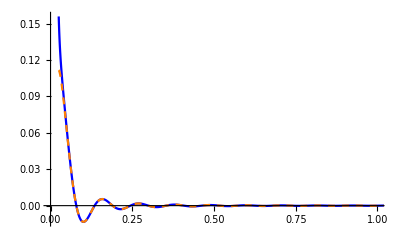
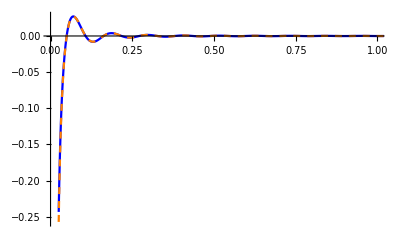
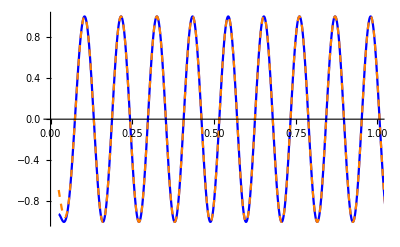
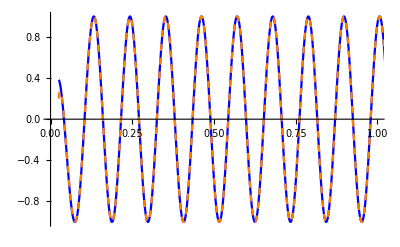
k=100 | Re | Im
ψ | -Graphics- | -Graphics-
δ_r | -Graphics- | -Graphics-

```mathematica
displaynumericalpsir[ψappr,δrappr,100,0.025,1.2,{{0,1},Full},{{0,1},Full}]
```

For the function in the next line, the INPUTS are as for displaynumericalpsir, with an additional final INPUT which control the %tage error graphed by the dashed line.

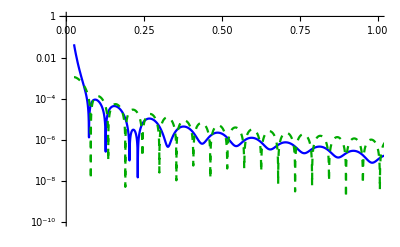
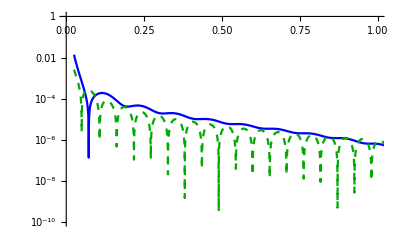
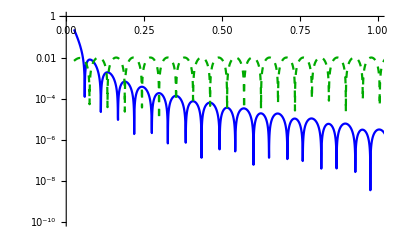
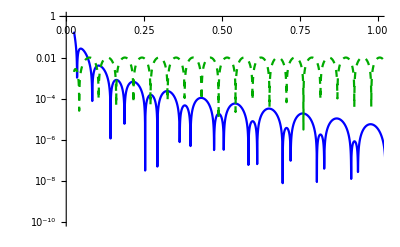
k=100
error line=1% | Re | Im
ψ | -Graphics- | -Graphics-
δ_r | -Graphics- | -Graphics-

```mathematica
displaynumericalerrorxpc[ψappr,δrappr,100,0.025,1.2,{{0,1},{10^-10,1}},{{0,1},{10^-10,1}},1]
```

For the function in the next line INPUT the ψ,δ_r and δ_m functions, followed by the value of k, the minimum and the maximum values of τ, and PlotRanges for the ψ,δ_r and δ_m  graphs.
There are additional optional arguments in the function’s definition, which are needed in the third order version.  They include the fifth order double power series to set up the initial conditions for the δ_m numerical solution properly

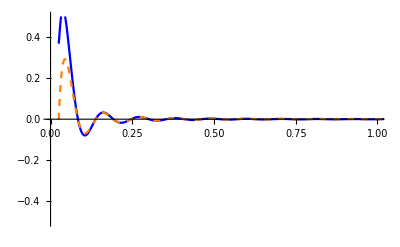
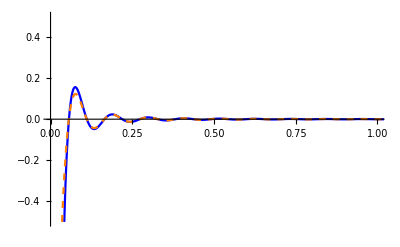
k=100 | ψ | δ_r | δ_m
Re | -Graphics- | -Graphics- | -Graphics-
Im | -Graphics- | -Graphics- | -Graphics-

```mathematica
Figrm100=displaynumericalpsirmat[ψappr,δrappr,δmappr,100,0.025,1.2,{{0,1},Full},{{0,1},Full},{{0,1},{-0.5,0.5}},"Yes",ψappr5,δrappr5]
```

```mathematica
(*Export["Figrm100.pdf",Figrm100];*)
```

For the function in the next line, the INPUTS are as for displaynumericalpsir, with an additional INPUT at argument number 10, which controls the %tage error graphed by the dashed line.

Note that the maximum value of τ in the next line is set to just above 1 to avoid spurious edge effects in the numerical solution.

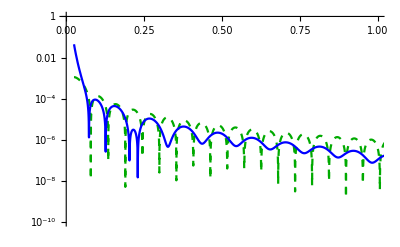
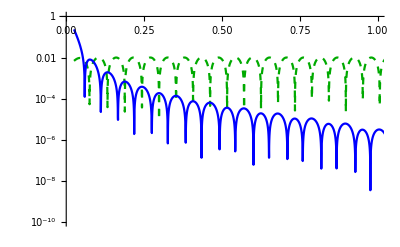
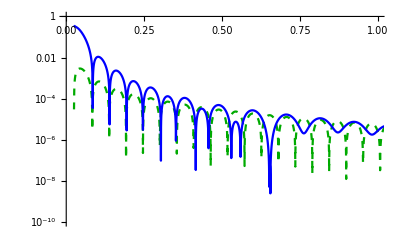
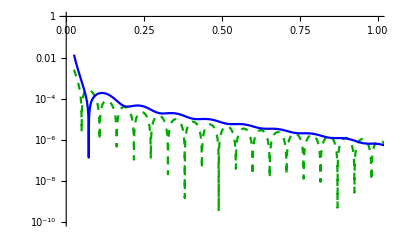
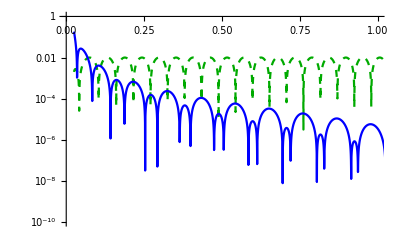
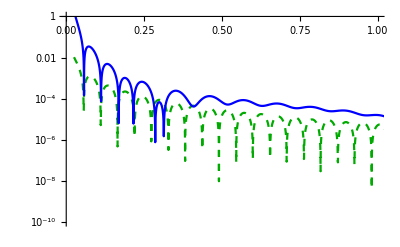
k=100
Dashes=1% | ψ | δ_r | δ_m
Re | -Graphics- | -Graphics- | -Graphics-
Im | -Graphics- | -Graphics- | -Graphics-

```mathematica
Figrm100error=displaynumericalerrorxpcmat[ψappr,δrappr,δmappr,100,0.025,1.2,{{0,1},{10^-10,1}},{{0,1},{10^-10,1}},{{0,1},{10^-10,1}},1,"Yes",ψappr5,δrappr5]
```

```mathematica
(*Export["Figrm100error.pdf",Figrm100error];*)
```

The following are the functions which support the above calculations.
They are all initialisation cells.

Functions for double power series calculations
These are generically adaptable for other suitable (systems of) differential equations.

```mathematica
displaymatrices[]:=Print[StringForm["A=``, B_-2=``, B_0=``, C=``",TraditionalForm[a],TraditionalForm[bm2],TraditionalForm[b0],TraditionalForm[c]]]
```

```mathematica
inspecteigenvalues[]:=If[Length[fncnames]>1,Eigenvalues[Inverse[a].bm2],{bm2/a}]
```

```mathematica
dimofmatrix[matrix_]:=Module[{},
If[Length[fncnames]==1&&Not[MatrixQ[matrix]],
Return[1],
If[
SquareMatrixQ[matrix],
Return[Dimensions[matrix][[1]]],
Return["Not square"]
]
]
]
```

```mathematica
dimsofmatrics[]:=Module[{dimsnames,dimlist=Thread[Unevaluated[dimofmatrix[{a,bm2,b0,c}]]]},
dimsnames=Length[fncnames];
Which[
MemberQ[dimlist,"Not square"],
Return["Error: using at least one non-square matrix"],
Or[Length[DeleteDuplicates[dimlist]]>1,dimlist[[1]]≠dimsnames ],Return["Error: matrices are square, but not all of the right number of dimensions"],
True,
Return[dimsnames]
]
]
```

```mathematica
errorcheck[message_]:=StringMatchQ[ToString[message],"Error*"]
```

```mathematica
eigenvaluecheck[eval_]:=Module[{roots=inspecteigenvalues[]},
Which[
Not[MemberQ[roots,eval]],Return["Error: The first argument is not an eigenvalue."],
eval==0,Return["Error: You have chosen a 0 eigenvalue."],
Count[roots,eval]>1,Return["Error: You have chosen a eigenvalue which is a repeated root of the characteristic equation."],
True,Return["OK: Valid eigenvalue"]
]
]
```

```mathematica
ruletosymbols[rl_]:=Module[{j},
Union[Table[rl[[j,1]],{j,1,Length[rl]}]]
]
```

```mathematica
lremove[var_]:=0
```

```mathematica
simplifytc[expn_]:=Simplify[expn,TimeConstraint->{10,10}]
```

```mathematica
DoublePowerSeriesMethod[eval_,maxs_,dims_]:=Module[{symbols,ω,p,ϵ,expsum,xexp0,xexp1,xexp2,eqnexp,eqnexptable,s,remainingsymbols,calculatedsymbols,rule,rndofs,zerovector,symbolstoone,rndeqnexp,rndrule,ωf,dim,pf,updaterule,rndsymbols,symbolstozero,expexpn,nologexpn,logexp,expfnc,fnc,fncexp},

symbols=Flatten[Union[Array[ω[τ],maxs+1, 0],Array[p[τ],{maxs+1,dims},{0,1}]]];
expsum[τ]=∑_(s=0)^maxs ϵ^(s-1)*ω[τ][s];
xexp0[τ]=Table[(∑_(s=0)^maxs ϵ^s*p[τ][s,dim]),{dim,1,dims}];
If[dims==1,xexp0[τ]=xexp0[τ][[1]]];xexp1[τ]=ϵ*(xexp0[τ]*expsum[τ]+D[xexp0[τ],τ]);xexp2[τ]=ϵ^2*(D[D[xexp0[τ],τ],τ]+2*D[xexp0[τ],τ]*expsum[τ]+xexp0[τ]*D[expsum[τ],τ]+xexp0[τ]*expsum[τ]^2);
If[dims==1,
eqnexp=a*(xexp2[τ]) +ϵ*c*(xexp1[τ])+(bm2+ϵ^2*b0)*(xexp0[τ]),
eqnexp=a.(xexp2[τ]) +ϵ*c.(xexp1[τ])+(bm2+ϵ^2*b0).(xexp0[τ])];
eqnexptable=Table[Coefficient[eqnexp,ϵ,s],{s,0,maxs}];

Clear[s];remainingsymbols=symbols;rule={ϵ->1/k};rndofs=1;zerovector=ConstantArray[0,dims];

ωf[0]=√-eval;
rndrule=If[dims==1,
{p[τ][0,1]->1},
Flatten[Quiet[Solve[(a*-eval+bm2).Table[p[τ][0,dim],{dim,1,dims}]==zerovector,remainingsymbols]]]];
calculatedsymbols=ruletosymbols[rndrule];
rndsymbols=Table[p[τ][0,dim],{dim,1,dims}];
symbolstoone=Complement[rndsymbols,calculatedsymbols];
rndrule=Join[rndrule,Thread[symbolstoone->1]];
For[dim=1,dim≤dims,dim++,
pf[0,dim]=(p[τ][0,dim]//.rndrule)
];
updaterule=Join[{ω[τ][0]->ωf[0]},Table[p[τ][0,dim]->pf[0,dim],{dim,1,dims}]];
rule=Union[rule,updaterule,D[updaterule,τ],D[D[updaterule,τ],τ]];

For[s=1,s≤maxs,s++,
rndeqnexp=eqnexptable[[s+rndofs]]//.rule;
rndrule=Flatten[Quiet[Solve[rndeqnexp==zerovector,remainingsymbols]]];
calculatedsymbols=ruletosymbols[rndrule];
rndsymbols=Join[{ω[τ][s]},Table[p[τ][s,dim],{dim,1,dims}]];
symbolstozero=Complement[rndsymbols,calculatedsymbols];
rndrule=Join[rndrule,Thread[symbolstozero->0]];
ωf[s]=ω[τ][s]//.rndrule;
For[dim=1,dim≤dims,dim++,
pf[s,dim]=p[τ][s,dim]//.rndrule];
updaterule=Join[{ω[τ][s]->ωf[s]},Table[p[τ][s,dim]->pf[s,dim],{dim,1,dims}]];
rule=Union[rule,updaterule,D[updaterule,τ],D[D[updaterule,τ],τ]]
];
expexpn=∫((∑_(s=0)^maxs k^(-s+1)*ωf[s]))ⅆτ;
nologexpn=Collect[expexpn/.{Log->lremove},k,simplifytc];
logexp=expexpn-nologexpn;
expfnc=Assuming[τ>0,simplifytc[Exp[logexp]]]*Exp[nologexpn];
Print[StringForm["E(τ)=``",expfnc]];

For[dim=1,dim≤dims,dim++,
fnc[dim]=Collect[((∑_(s=0)^maxs k^-s*pf[s,dim])),k,simplifytc];
Print[StringForm["``(τ)=``*E(τ)",fncnames[[dim]],{fnc[dim]}]];
fncexp[dim]=fnc[dim]*expfnc
];

Return[Table[fncexp[dim],{dim,1,dims}]]
]
```

```mathematica
runDoublePowerSeries[eval_,maxs_]:=Module[{dims=dimsofmatrics[],evalstatus},
Which[
errorcheck[dims],Print[dims],
errorcheck[evalstatus=eigenvaluecheck[eval]],Print[evalstatus],
Or[Not[IntegerQ[maxs]],maxs<0],Print["Error: the maximum value of s must be a non-negative integer."],
True,DoublePowerSeriesMethod[eval,maxs,dims]
]
]
```

Function for matter calculation

```mathematica
δmcalculate[ψfn_,δrfn_,δrfnmult_,nterms_]:=Module[{δm},
δm=(Normal[Series[Expand[((-6/(τ*(4+τ))*δrfn[τ])^-1*(3*((2*(2+τ))/(τ*(4+τ)))*ψfn'[τ]+(3*((2*(2+τ))/(τ*(4+τ)))^2+k^2)*ψfn[τ]+3/2*(4/(τ*(4+τ)))^2*δrfn[τ]))/.k->ϵ^-1],{ϵ,0,nterms}]]/.ϵ->k^-1)*δrfnmult[τ];
Print[δm];
Return[δm]
]
```

Display functions

```mathematica
imsz="Medium";
```

```mathematica
axslab={"τ",Automatic};
```

```mathematica
ao={0,0};
```

```mathematica
axsticks={Automatic,Automatic};
```

```mathematica
laxsticks={Automatic,Join[Table[{10^i,Superscript[10,i]},{i,-10,1,2}],{{10,Superscript[10,1]}}]};
```

```mathematica
padding={{30,30},{10,10}};
```

```mathematica
τeq=2*(√2-1);τhor=(1-2 k+√(1+4 k^2))/k;τdrag=1.73022;gl={{{τhor,{Dashed,Thick}},{τeq,Thick},{τdrag,{Thick,Lighter[Red,0.6]}}},None};
```

```mathematica
displaynumericalpsir[ψfn_,δrfn_,kdisplay_,τmin_,τmax_,rangeψ_,rangeδr_]:=Module[{ψsol,δrsol,disprule},
disprule={τ->τmax,k->kdisplay};
ψval=Evaluate[ψfn[τ]//.disprule];
δrval=Evaluate[δrfn[τ]//.disprule];
dψval=Evaluate[ψfn'[τ]//.disprule];
dδrval=Evaluate[(δrfn'[τ])//.disprule];
eqnmatrix=(1/k^2*a.D[D[{ψ[τ],δr[τ]},τ],τ]+1/k^2*c.D[{ψ[τ],δr[τ]},τ]+(bm2+1/k^2*b0).{ψ[τ],δr[τ]})//.k->kdisplay;
nsoln=NDSolve[{eqnmatrix=={0,0},ψ[τmax]==ψval,δr[τmax]==δrval,ψ'[τmax]==dψval,δr'[τmax]==dδrval},{ψ[τ],δr[τ]},{τ,τmin,τmax}];
ψsol[τ_]:=Evaluate[ψ[τ]/.nsoln];
δrsol[τ_]:=Evaluate[δr[τ]/.nsoln];
ψdisp[τ_]:=ψfn[τ]/.k->kdisplay;
δrdisp[τ_]:=δrfn[τ]/.k->kdisplay;
Grid[{{Style[StringForm["k=``",kdisplay]],"Re","Im"},
{fncnames[[1]],
Plot[{Re[ψdisp[τ]],Re[ψsol[τ]]},{τ,τmin,τmax},PlotStyle->{{Blue,Automatic},{Orange,Dashed}},PlotRange->rangeψ,ImageSize->imsz,FrameLabel->axslab,FrameTicks->axsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding],
Plot[{Im[ψdisp[τ]],Im[ψsol[τ]]},{τ,τmin,τmax},PlotStyle->{{Blue,Automatic},{Orange,Dashed}},PlotRange->rangeψ,ImageSize->imsz,FrameLabel->axslab,FrameTicks->axsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding]},
{fncnames[[2]],
Plot[{Re[δrdisp[τ]],Re[δrsol[τ]]},{τ,τmin,τmax},PlotStyle->{{Blue,Automatic},{Orange,Dashed}},PlotRange->rangeδr,ImageSize->imsz,FrameLabel->axslab,FrameTicks->axsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding],
Plot[{Im[δrdisp[τ]],Im[δrsol[τ]]},{τ,τmin,τmax},PlotStyle->{{Blue,Automatic},{Orange,Dashed}},PlotRange->rangeδr,ImageSize->imsz,FrameLabel->axslab,FrameTicks->axsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding]
}}]]
```

```mathematica
displaynumericalerrorxpc[ψfn_,δrfn_,kdisplay_,τmin_,τmax_,rangeψ_,rangeδr_,pc_]:=Module[{ψsol,δrsol,disprule},
disprule={τ->τmax,k->kdisplay};
ψval=Evaluate[ψfn[τ]//.disprule];
δrval=Evaluate[δrfn[τ]//.disprule];
dψval=Evaluate[ψfn'[τ]//.disprule];
dδrval=Evaluate[δrfn'[τ]//.disprule];
eqnmatrix=(1/k^2*a.D[D[{ψ[τ],δr[τ]},τ],τ]+1/k^2*c.D[{ψ[τ],δr[τ]},τ]+(bm2+1/k^2*b0).{ψ[τ],δr[τ]})//.k->kdisplay;
nsoln=NDSolve[{eqnmatrix=={0,0},ψ[τmax]==ψval,δr[τmax]==δrval,ψ'[τmax]==dψval,δr'[τmax]==dδrval},{ψ[τ],δr[τ]},{τ,τmin,τmax}];
ψsol[τ_]:=Evaluate[ψ[τ]/.nsoln];
δrsol[τ_]:=Evaluate[δr[τ]/.nsoln];
ψdisp[τ_]:=ψfn[τ]/.k->kdisplay;
δrdisp[τ_]:=δrfn[τ]/.k->kdisplay;
Grid[{{Style[StringForm["k=``\nerror line=``%",kdisplay,pc]],"Re","Im"},
{fncnames[[1]],
LogPlot[{Abs[Re[ψsol[τ]-ψdisp[τ]]],Abs[Re[pc*ψsol[τ]/100]]},{τ,τmin,τmax},PlotStyle->(psty={{Blue,Automatic},{Darker[Green],Dashed}}),PlotRange->rangeψ,ImageSize->imsz,Ticks->laxsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding],
LogPlot[{Abs[Im[ψsol[τ]-ψdisp[τ]]],Abs[pc*Im[ψsol[τ]/100]]},{τ,τmin,τmax},PlotStyle->psty,PlotRange->rangeψ,ImageSize->imsz,Ticks->laxsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding]
},
{fncnames[[2]],
LogPlot[{Abs[Re[δrsol[τ]-δrdisp[τ]]],Abs[pc*Re[δrsol[τ]/100]]},{τ,τmin,τmax},PlotStyle->psty,PlotRange->rangeδr,ImageSize->imsz,Ticks->laxsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding],
LogPlot[{Abs[Im[δrsol[τ]-δrdisp[τ]]],Abs[Im[pc*δrsol[τ]/100]]},{τ,τmin,τmax},PlotStyle->psty,PlotRange->rangeδr,ImageSize->imsz,Ticks->laxsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding]
}
}]]
```

```mathematica
displaynumericalpsirmat[ψfn_,δrfn_,δmfn_,kdisplay_,τmin_,τmax_,rangeψ_,rangeδr_,rangeδm_,diff_:"No",ψseed_:"default",δrseed_:"default"]:=Module[{ψsol,δrsol,ψsolseed,δrsolseed,δmsol,disprule},
disprule={τ->τmax,k->kdisplay};
ψval=Evaluate[ψfn[τ]//.disprule];
δrval=Evaluate[δrfn[τ]//.disprule];
dψval=Evaluate[ψfn'[τ]//.disprule];
dδrval=Evaluate[(δrfn'[τ])//.disprule];
eqnmatrix=(1/k^2*a.D[D[{ψ[τ],δr[τ]},τ],τ]+1/k^2*c.D[{ψ[τ],δr[τ]},τ]+(bm2+1/k^2*b0).{ψ[τ],δr[τ]})//.k->kdisplay;
nsoln=NDSolve[{eqnmatrix=={0,0},ψ[τmax]==ψval,δr[τmax]==δrval,ψ'[τmax]==dψval,δr'[τmax]==dδrval},{ψ[τ],δr[τ]},{τ,τmin,τmax}];
ψsol[τ_]:=Evaluate[ψ[τ]/.nsoln];
δrsol[τ_]:=Evaluate[δr[τ]/.nsoln];

If[diff!="No",
ψvalseed=Evaluate[ψseed[τ]//.disprule];
δrvalseed=Evaluate[δrseed[τ]//.disprule];
dψvalseed=Evaluate[ψseed'[τ]//.disprule];
dδrvalseed=Evaluate[(δrseed'[τ])//.disprule];nsolnseed=NDSolve[{eqnmatrix=={0,0},ψ[τmax]==ψvalseed,δr[τmax]==δrvalseed,ψ'[τmax]==dψvalseed,δr'[τmax]==dδrvalseed},{ψ[τ],δr[τ]},{τ,τmin,τmax}];
ψsolseed[τ_]:=Evaluate[ψ[τ]/.nsolnseed];
δrsolseed[τ_]:=Evaluate[δr[τ]/.nsolnseed],
ψsolseed[τ_]:=ψsol[τ];
δrsolseed[τ_]:=δrsol[τ];
];
δmsol[τ_]:=Evaluate[((-6/(τ*(4+τ)))^-1*(3*((2*(2+τ))/(τ*(4+τ)))*ψsolseed'[τ]+(3*((2*(2+τ))/(τ*(4+τ)))^2+k^2)*ψsolseed[τ]+3/2*(4/(τ*(4+τ)))^2*δrsolseed[τ]))[[1]]/.{k->kdisplay}];
ψdisp[τ_]:=ψfn[τ]/.k->kdisplay;
δrdisp[τ_]:=δrfn[τ]/.k->kdisplay;
δmdisp[τ_]:=δmfn[τ]/.k->kdisplay;

Grid[Transpose[{{Style[StringForm["    k=``",kdisplay]],"Re","Im"},
{fncnames[[1]],
Plot[{Re[ψdisp[τ]],Re[ψsol[τ]]},{τ,τmin,τmax},PlotStyle->{{Blue,Automatic},{Orange,Dashed}},PlotRange->rangeψ,ImageSize->imsz,FrameLabel->axslab,FrameTicks->axsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding],
Plot[{Im[ψdisp[τ]],Im[ψsol[τ]]},{τ,τmin,τmax},PlotStyle->{{Blue,Automatic},{Orange,Dashed}},PlotRange->rangeψ,ImageSize->imsz,FrameLabel->axslab,FrameTicks->axsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding]},
{fncnames[[2]],
Plot[{Re[δrdisp[τ]],Re[δrsol[τ]]},{τ,τmin,τmax},PlotStyle->{{Blue,Automatic},{Orange,Dashed}},PlotRange->rangeδr,ImageSize->imsz,FrameLabel->axslab,FrameTicks->axsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding],
Plot[{Im[δrdisp[τ]],Im[δrsol[τ]]},{τ,τmin,τmax},PlotStyle->{{Blue,Automatic},{Orange,Dashed}},PlotRange->rangeδr,ImageSize->imsz,FrameLabel->axslab,FrameTicks->axsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding]},
{"δ_m",
Plot[{Re[δmdisp[τ]],Re[δmsol[τ]]},{τ,τmin,τmax},PlotStyle->{{Blue,Automatic},{Orange,Dashed}},PlotRange->rangeδm,ImageSize->imsz,FrameLabel->axslab,FrameTicks->axsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding],
Plot[{Im[δmdisp[τ]],Im[δmsol[τ]]},{τ,τmin,τmax},PlotStyle->{{Blue,Automatic},{Orange,Dashed}},PlotRange->rangeδm,ImageSize->imsz,FrameLabel->axslab,FrameTicks->axsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding]
}}]]
]
```

```mathematica
displaynumericalerrorxpcmat[ψfn_,δrfn_,δmfn_,kdisplay_,τmin_,τmax_,rangeψ_,rangeδr_,rangeδm_,pc_,diff_:"No",ψseed_:"default",δrseed_:"default"]:=Module[{ψsol,δrsol,ψsolseed,δrsolseed,δmsol,disprule},
disprule={τ->τmax,k->kdisplay};
ψval=Evaluate[ψfn[τ]//.disprule];
δrval=Evaluate[δrfn[τ]//.disprule];
dψval=Evaluate[ψfn'[τ]//.disprule];
dδrval=Evaluate[δrfn'[τ]//.disprule];
eqnmatrix=(1/k^2*a.D[D[{ψ[τ],δr[τ]},τ],τ]+1/k^2*c.D[{ψ[τ],δr[τ]},τ]+(bm2+1/k^2*b0).{ψ[τ],δr[τ]})//.k->kdisplay;
nsoln=NDSolve[{eqnmatrix=={0,0},ψ[τmax]==ψval,δr[τmax]==δrval,ψ'[τmax]==dψval,δr'[τmax]==dδrval},{ψ[τ],δr[τ]},{τ,τmin,τmax}];
ψsol[τ_]:=Evaluate[ψ[τ]/.nsoln];
δrsol[τ_]:=Evaluate[δr[τ]/.nsoln];

If[diff!="No",
ψvalseed=Evaluate[ψseed[τ]//.disprule];
δrvalseed=Evaluate[δrseed[τ]//.disprule];
dψvalseed=Evaluate[ψseed'[τ]//.disprule];
dδrvalseed=Evaluate[(δrseed'[τ])//.disprule];nsolnseed=NDSolve[{eqnmatrix=={0,0},ψ[τmax]==ψvalseed,δr[τmax]==δrvalseed,ψ'[τmax]==dψvalseed,δr'[τmax]==dδrvalseed},{ψ[τ],δr[τ]},{τ,τmin,τmax}];
ψsolseed[τ_]:=Evaluate[ψ[τ]/.nsolnseed];
δrsolseed[τ_]:=Evaluate[δr[τ]/.nsolnseed],
ψsolseed[τ_]:=ψsol[τ];
δrsolseed[τ_]:=δrsol[τ];
];
δmsol[τ_]:=Evaluate[((-6/(τ*(4+τ)))^-1*(3*((2*(2+τ))/(τ*(4+τ)))*ψsolseed'[τ]+(3*((2*(2+τ))/(τ*(4+τ)))^2+k^2)*ψsolseed[τ]+3/2*(4/(τ*(4+τ)))^2*δrsolseed[τ]))[[1]]/.{k->kdisplay}];
ψdisp[τ_]:=ψfn[τ]/.k->kdisplay;
δrdisp[τ_]:=δrfn[τ]/.k->kdisplay;
δmdisp[τ_]:=δmfn[τ]/.k->kdisplay;
Grid[Transpose[{{Style[StringForm["    k=``\nDashes=``%",kdisplay,pc]],"Re","Im"},
{fncnames[[1]],
LogPlot[{Abs[Re[pc*ψsol[τ]/100]],Abs[Re[ψsol[τ]-ψdisp[τ]]]},{τ,τmin,τmax},PlotStyle->(psty={{Darker[Green],Dashed},{Blue,Automatic}}),PlotRange->rangeψ,ImageSize->imsz,Ticks->laxsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding],
LogPlot[{Abs[pc*Im[ψsol[τ]/100]],Abs[Im[ψsol[τ]-ψdisp[τ]]]},{τ,τmin,τmax},PlotStyle->psty,PlotRange->rangeψ,ImageSize->imsz,Ticks->laxsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding]
},
{fncnames[[2]],
LogPlot[{Abs[pc*Re[δrsol[τ]/100]],Abs[Re[δrsol[τ]-δrdisp[τ]]]},{τ,τmin,τmax},PlotStyle->psty,PlotRange->rangeδr,ImageSize->imsz,Ticks->laxsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding],
LogPlot[{Abs[Im[pc*δrsol[τ]/100]],Abs[Im[δrsol[τ]-δrdisp[τ]]]},{τ,τmin,τmax},PlotStyle->psty,PlotRange->rangeδr,ImageSize->imsz,Ticks->laxsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding]
},
{"δ_m",
LogPlot[{Abs[pc*Re[δmsol[τ]/100]],Abs[Re[δmsol[τ]-δmdisp[τ]]]},{τ,τmin,τmax},PlotStyle->psty,PlotRange->rangeδm,ImageSize->imsz,Ticks->laxsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding],
LogPlot[{Abs[Im[pc*δmsol[τ]/100]],Abs[Im[δmsol[τ]-δmdisp[τ]]]},{τ,τmin,τmax},PlotStyle->psty,PlotRange->rangeδm,ImageSize->imsz,Ticks->laxsticks,AxesOrigin->ao,GridLines->Evaluate[gl/.k->kdisplay],ImagePadding->padding]
}
}]]
]
```